```mathematica
gateVar1=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar1.csv"];
gateVar2=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar2.csv"];
gateVar3=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar3.csv"];
gateVar4=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar4.csv"];
gateVar5=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar5.csv"];
gateVar6=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar6.csv"];
gateVar7=Import["D:\OneDrive\Mathematica\HT_soi_dn\IV-soi-dn-gateVar7.csv"];
(*TableForm[data[[1;;-1]]];*)
```

```mathematica
Select[data,#[[3]]=="Anode Current"&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[data,#1⟦3⟧==Anode Current&].

Select[data,#1⟦3⟧==Anode Current&]

```mathematica
data[[3]];
```

Part::partd: Part specification data⟦3⟧ is longer than depth of object.

```mathematica
data2=Select[data,#[[3]]=="Anode Current"&][[All,{1,3,-3}]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[data,#1⟦3⟧==Anode Current&].

Part::partd: Part specification Select[data,#1⟦3⟧==Anode Current&]⟦All,{1,3,-3}⟧ is longer than depth of object.

Select[data,#1⟦3⟧==Anode Current&]⟦All,{1,3,-3}⟧

```mathematica
data3=GroupBy[data2,#[[2]]&,#[[All,{1,2}]]&]
```

GroupBy::list1: The argument Select[data,#1⟦3⟧==Anode Current&]⟦All,{1,3,-3}⟧ is not a valid list of Associations or rules or lists of rules.

GroupBy[Select[data,#1⟦3⟧==Anode Current&]⟦All,{1,3,-3}⟧,#1⟦2⟧&,#1⟦All,{1,2}⟧&]

```mathematica
data1=data[[39;;-1]];data1[[All,{1,3}]];ListLinePlot[data1[[All,{1,3}]]]
```

Part::take: Cannot take positions 39 through -1 in data.

Part::partd: Part specification data⟦39;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: data⟦39;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[data⟦39;;-1⟧⟦All,{1,3}⟧]

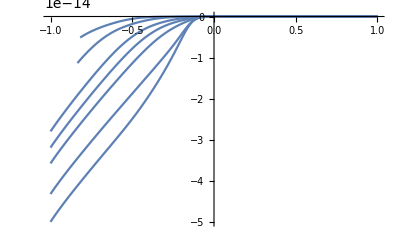

```mathematica
dat1=gateVar1[[39;;-1]];dat2=gateVar2[[18;;-1]];dat3=gateVar3[[3;;-1]];dat4=gateVar4[[3;;-1]];dat5=gateVar5[[3;;-1]];dat6=gateVar6[[3;;-1]];dat7=gateVar7[[3;;-1]];
ListLinePlot[dat2[[All,{1,3}]]];ListLinePlot[dat3[[All,{1,3}]]];ListLinePlot[dat7[[All,{1,3}]]];
Show[ListLinePlot[dat1[[All,{1,3}]]],ListLinePlot[dat2[[All,{1,3}]]],ListLinePlot[dat3[[All,{1,3}]]],ListLinePlot[dat4[[All,{1,3}]]],ListLinePlot[dat5[[All,{1,3}]]],ListLinePlot[dat6[[All,{1,3}]]],ListLinePlot[dat7[[All,{1,3}]]],PlotRange->{{-1,1},{0,-5 10^-14}}]
```

```mathematica
dat2[[All,{1,3}]];
```

```mathematica
$HomeDirectory;Directory[];
gateVar1=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar1.csv"];
gateVar2=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar2.csv"];
gateVar3=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar3.csv"];
gateVar4=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar4.csv"];
gateVar5=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar5.csv"];
gateVar6=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar6.csv"];
gateVar7=Import["/data/onedrive/HT_soi_dn/IV-soi-dn-gateVar7.csv"];
dat1=gateVar1[[39;;-1]];
dat2=gateVar2[[18;;-1]];
dat3=gateVar3[[3;;-1]];dat4=gateVar4[[3;;-1]];dat5=gateVar5[[3;;-1]];dat6=gateVar6[[3;;-1]];dat7=gateVar7[[3;;-1]];
ListLinePlot[dat2[[All,{1,3}]]];ListLinePlot[dat3[[All,{1,3}]]];ListLinePlot[dat7[[All,{1,3}]]];
```

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar1.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar2.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar3.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar4.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar5.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar6.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dn/IV-soi-dn-gateVar7.csv not found during Import.

Part::take: Cannot take positions 39 through -1 in $Failed.

Part::take: Cannot take positions 18 through -1 in $Failed.

Part::take: Cannot take positions 3 through -1 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦18;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦18;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Show[ListLinePlot[dat1[[All,{1,3}]]],ListLinePlot[dat2[[All,{1,3}]]],ListLinePlot[dat3[[All,{1,3}]]],ListLinePlot[dat4[[All,{1,3}]]],ListLinePlot[dat5[[All,{1,3}]]],ListLinePlot[dat6[[All,{1,3}]]],ListLinePlot[dat7[[All,{1,3}]]],PlotRange->{{-0.8,0.8},{0,-5 10^-14}},Frame->True,FrameLabel->{"Anode Voltage [V]","Anode Current [A]"},PlotLabel->"I-V Charateristics of SOI-dn device model with SILVACO TCAD",FontFamily->"Times",PlotLegends->Automatic]
```

Part::partd: Part specification $Failed⟦39;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦39;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦18;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦18;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[$Failed⟦39;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦18;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],PlotRange→{{-0.8,0.8},{0,-1/20000000000000}},Frame→True,FrameLabel→{Anode Voltage [V],Anode Current [A]},«3»].

Show[ListLinePlot[$Failed⟦39;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦18;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦3;;-1⟧⟦All,{1,3}⟧],PlotRange→{{-0.8,0.8},{0,-1/20000000000000}},Frame→True,FrameLabel→{Anode Voltage [V],Anode Current [A]},PlotLabel→I-V Charateristics of SOI-dn device model with SILVACO TCAD,FontFamily→Times,PlotLegends→Automatic]

```mathematica
gateVar1=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar1.csv"];
gateVar2=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar2.csv"];
gateVar3=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar3.csv"];
gateVar4=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar4.csv"];
gateVar5=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar5.csv"];
gateVar6=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar6.csv"];
gateVar7=Import["/data/onedrive/HT_soi_dp/soi-dn-gateVar7.csv"];
dat1=gateVar1[[39;;-1]];
dat2=gateVar2[[18;;-1]];
dat3=gateVar3[[3;;-1]];dat4=gateVar4[[3;;-1]];dat5=gateVar5[[3;;-1]];dat6=gateVar6[[3;;-1]];dat7=gateVar7[[3;;-1]];
ListLinePlot[dat2[[All,{1,3}]]];ListLinePlot[dat3[[All,{1,3}]]];ListLinePlot[dat7[[All,{1,3}]]];
```

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar1.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar2.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar3.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar4.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar5.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar6.csv not found during Import.

Import::nffil: File /data/onedrive/HT_soi_dp/soi-dn-gateVar7.csv not found during Import.

Part::take: Cannot take positions 39 through -1 in $Failed.

Part::take: Cannot take positions 18 through -1 in $Failed.

Part::take: Cannot take positions 3 through -1 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦18;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦18;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: $Failed⟦3;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
Import["D:\\000_LAB_Result\SILVACO\soi_dp\soi_dn_gateVar4.csv"];
data00=%[[6;;-1]];
Import["D:\\000_LAB_Result\SILVACO\soi_dp\soi_dn_gateVar6.csv"];
data03=%[[6;;-1]];
Show[ListLinePlot[data03[[All,{1,3}]]],ListLinePlot[data00[[All,{1,3}]]],PlotRange->{{-5,5},{10^-13,-1 10^-13}},Frame->True,FrameLabel->{"Anode Voltage [V]","Anode Current [A]"},PlotLabel->"I-V Charateristics of SOI-dn device model with SILVACO TCAD",PlotLegends->Automatic]
```

Import::nffil: File D:\000_LAB_Result\SILVACO\soi_dp\soi_dn_gateVar4.csv not found during Import.

Part::take: Cannot take positions 6 through -1 in $Failed.

Import::nffil: File D:\000_LAB_Result\SILVACO\soi_dp\soi_dn_gateVar6.csv not found during Import.

Part::take: Cannot take positions 6 through -1 in $Failed.

Part::partd: Part specification $Failed⟦6;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦6;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification $Failed⟦6;;-1⟧⟦All,{1,3}⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: $Failed⟦6;;-1⟧⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[$Failed⟦6;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦6;;-1⟧⟦All,{1,3}⟧],PlotRange→{{-5,5},{1/10000000000000,-1/10000000000000}},Frame→True,FrameLabel→{Anode Voltage [V],Anode Current [A]},PlotLabel→I-V Charateristics of SOI-dn device model with SILVACO TCAD,PlotLegends→Automatic].

Show[ListLinePlot[$Failed⟦6;;-1⟧⟦All,{1,3}⟧],ListLinePlot[$Failed⟦6;;-1⟧⟦All,{1,3}⟧],PlotRange→{{-5,5},{1/10000000000000,-1/10000000000000}},Frame→True,FrameLabel→{Anode Voltage [V],Anode Current [A]},PlotLabel→I-V Charateristics of SOI-dn device model with SILVACO TCAD,PlotLegends→Automatic]

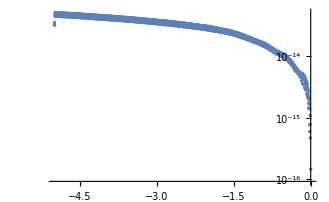

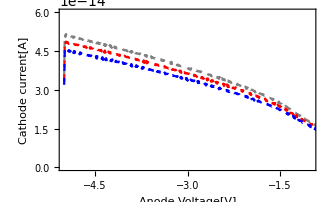

```mathematica
Pdata04=Import["D:\\000_LAB_Result\SILVACO\soi_dp\ic-va_soi_dp_gateVar4.csv"];PdataGate00=Pdata04[[5;;-1]];
Pdata05=Import["D:\\000_LAB_Result\SILVACO\soi_dp\ic-va_soi_dp_gateVar5.csv"];PdataGate01=Pdata05[[5;;-1]];
Pdata07=Import["D:\\000_LAB_Result\SILVACO\soi_dp\ic-va_soi_dp_gateVar7.csv"];PdataGate05=Pdata07[[5;;-1]];
ListLinePlot[PdataGate00[[All,{1,6}]]];ListLinePlot[PdataGate01[[All,{1,6}]]];
Show[ListLogPlot[PdataGate00[[All,{1,6}]]],ListLogPlot[PdataGate01[[All,{1,6}]]],ListLogPlot[PdataGate05[[All,{1,6}]]],PlotTheme->"Scientific"]
Show[ListLinePlot[PdataGate00[[All,{1,6}]],PlotStyle->{Gray,Dashed}],ListLinePlot[PdataGate01[[All,{1,6}]],PlotStyle->{Red,Dashed}],ListLinePlot[PdataGate05[[All,{1,6}]],PlotStyle->{Blue,Dashed}],PlotRange->{{-5,-1},{0,0.6 10^-13}},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Anode Voltage[V]","Cathode current[A]"},PlotLegends->{"Gate=0","Gate=1","Gate=5"}]
(*Show[ListLinePlot[Pdata00[[All,{1,3}]]],ListLinePlot[Pdata01[[All,{1,3}]]],PlotRange->{{-5,5},{-10^-13,10^-10}},Frame->True,FrameLabel->{"Anode Voltage [V]","Anode Current [A]"},PlotLabel->"I-V Charateristics of SOI-dn device model with SILVACO TCAD"]
```

```mathematica
Manipulate[lplot[PdataGate00[[All,{1,6}]],PlotStyle->{Gray}],{lplot,{ListPlot,ListLinePlot,ListLogPlot,ListLogLogPlot}},Initialization:>({PdataGate00[[All,{1,6}]]})]
```

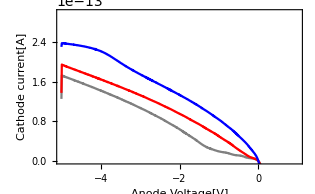

```mathematica
Ndata04=Import["D:\\000_LAB_Result\SILVACO\soi_dn\ic-va_soi_dn_gateVar4.csv"];NdataGate00=Ndata04[[5;;-1]];
Ndata05=Import["D:\\000_LAB_Result\SILVACO\soi_dn\ic-va_soi_dn_gateVar5.csv"];NdataGate01=Ndata05[[5;;-1]];
Ndata07=Import["D:\\000_LAB_Result\SILVACO\soi_dn\ic-va_soi_dn_gateVar7.csv"];NdataGate05=Ndata07[[5;;-1]];
ListLinePlot[NdataGate00[[All,{1,6}]],PlotRange->{{-5,1},{0,2 10^-13}}];
Show[ListLinePlot[NdataGate00[[All,{1,6}]],PlotStyle->{Gray}],ListLinePlot[NdataGate01[[All,{1,6}]],PlotStyle->{Red}],ListLinePlot[NdataGate05[[All,{1,6}]],PlotStyle->{Blue}],PlotRange->{{-5,1},{0,3 10^-13}},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Anode Voltage[V]","Cathode current[A]"},PlotLegends->{"Gate=0","Gate=1","Gate=5"}]
```

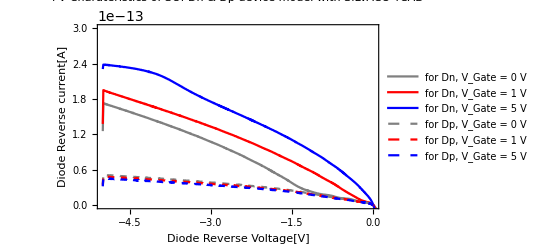

```mathematica
Show[ListLinePlot[NdataGate00[[All,{1,6}]],PlotStyle->{Gray},PlotLegends->{"for Dn, V_Gate = 0 V"}],ListLinePlot[NdataGate01[[All,{1,6}]],PlotStyle->{Red},PlotLegends->{"for Dn, V_Gate = 1 V"}],ListLinePlot[NdataGate05[[All,{1,6}]],PlotStyle->{Blue},PlotLegends->{"for Dn, V_Gate = 5 V"}],ListLinePlot[PdataGate00[[All,{1,6}]],PlotStyle->{Gray,Dashed},PlotLegends->{"for Dp, V_Gate = 0 V"}],ListLinePlot[PdataGate01[[All,{1,6}]],PlotStyle->{Red,Dashed},PlotLegends->{"for Dp, V_Gate = 1 V"}],ListLinePlot[PdataGate05[[All,{1,6}]],PlotStyle->{Blue,Dashed},PlotLegends->{"for Dp, V_Gate = 5 V"}],PlotRange->{{-5,0},{0,3 10^-13}},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Diode Reverse Voltage[V]","Diode Reverse current[A]"},PlotLabel->"I-V Charateristics of SOI-Dn & Dp device model with SILVACO TCAD"]
```

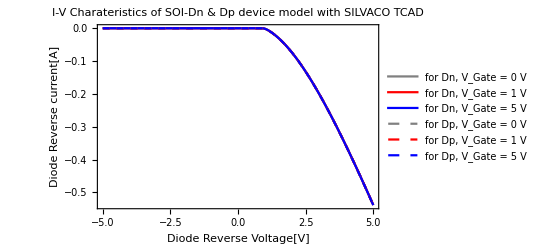

```mathematica
Show[ListLinePlot[NdataGate00[[All,{1,6}]],PlotStyle->{Gray},PlotLegends->{"for Dn, V_Gate = 0 V"}],ListLinePlot[NdataGate01[[All,{1,6}]],PlotStyle->{Red},PlotLegends->{"for Dn, V_Gate = 1 V"}],ListLinePlot[NdataGate05[[All,{1,6}]],PlotStyle->{Blue},PlotLegends->{"for Dn, V_Gate = 5 V"}],ListLinePlot[PdataGate00[[All,{1,6}]],PlotStyle->{Gray,Dashed},PlotLegends->{"for Dp, V_Gate = 0 V"}],ListLinePlot[PdataGate01[[All,{1,6}]],PlotStyle->{Red,Dashed},PlotLegends->{"for Dp, V_Gate = 1 V"}],ListLinePlot[PdataGate05[[All,{1,6}]],PlotStyle->{Blue,Dashed},PlotLegends->{"for Dp, V_Gate = 5 V"}],PlotRange->{{0,1},{0,-3 10^-3}},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Diode Reverse Voltage[V]","Diode Reverse current[A]"},PlotLabel->"I-V Charateristics of SOI-Dn & Dp device model with SILVACO TCAD"]
```

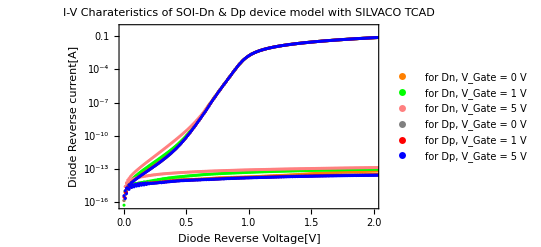

```mathematica
Show[ListLogPlot[Abs[NdataGate00[[All,{1,6}]]],PlotStyle->{Orange},PlotLegends->{"for Dn, V_Gate = 0 V"}],ListLogPlot[Abs[NdataGate01[[All,{1,6}]]],PlotStyle->{Green},PlotLegends->{"for Dn, V_Gate = 1 V"}],ListLogPlot[Abs[NdataGate05[[All,{1,6}]]],PlotStyle->{Pink},PlotLegends->{"for Dn, V_Gate = 5 V"}],ListLogPlot[Abs[PdataGate00[[All,{1,6}]]],PlotStyle->{Gray,Dashed},PlotLegends->{"for Dp, V_Gate = 0 V"}],ListLogPlot[Abs[PdataGate01[[All,{1,6}]]],PlotStyle->{Red,Dashed},PlotLegends->{"for Dp, V_Gate = 1 V"}],ListLogPlot[Abs[PdataGate05[[All,{1,6}]]],PlotStyle->{Blue,Dashed},PlotLegends->{"for Dp, V_Gate = 5 V"}],PlotRange->{{0,2},All},Frame->True,PlotTheme->"Scientific",FrameLabel->{"Diode Reverse Voltage[V]","Diode Reverse current[A]"},PlotLabel->"I-V Charateristics of SOI-Dn & Dp device model with SILVACO TCAD"]
```